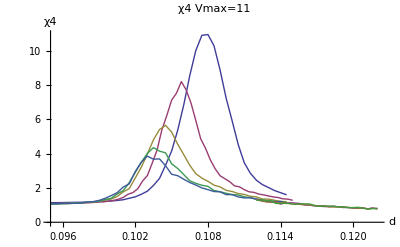

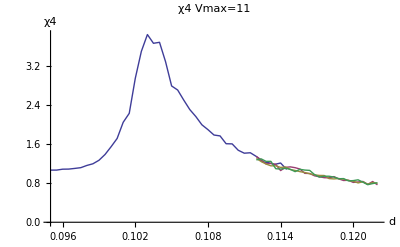

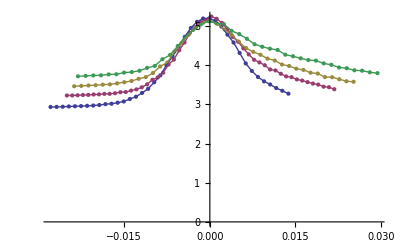

```mathematica
v=7;
ListLinePlot[{Ch4[v][2],Ch4[v][5],Ch4[v][10],Ch4[v][20],Ch4[v][40],Ch4[v][60],Ch4[v][80],Ch4[v][100]},PlotRange->Full,PlotLabel->"χ4 Vmax=11",AxesLabel->{"d","χ4"}]
ListLinePlot[{Ch4[v][40],Ch4[v][60],Ch4[v][80],Ch4[v][100]},PlotRange->Full,PlotLabel->"χ4 Vmax=11",AxesLabel->{"d","χ4"}]

ClearAll[d0,β,b,β2,b2,α,z]
d0[11]=0.06576996509783684;
β[11]=0.330373282657935;
b[11]=10^-2.2955586343397165;
β2[11]=0.33;
b2[11]=0.10036668471234145;
α[11]=0.6216439922507675;

d0[7]=0.10129517685639909;
β[7]=0.46313980302928304;
b[7]=10^-1.4905530421745141;
β2[7]=0.47;
b2[7]=0.2407530406366698;
α[7]=0.36868448770421297;

z[v]=0.1;


Do[
Ch4s2[v][l]=Table[{(Ch4[v][l][[All,1]][[i]]-d0[v]-b2[v]*(l*1000)^(-β2[v]))*(l*1000)^z[v],Log[Ch4[v][l][[All,2]][[i]]]+α[v]*Log[1000*l]},{i,1,Length[Ch4[v][l]]}];

Cht4s2[v][l]=Table[{(Cht4[v][l][[All,1]][[i]]-d0[v]-b2[v]*(l*1000)^(-β2[v]))*(l*1000)^z[v],Log[Cht4[v][l][[All,2]][[i]]]+α[v]*Log[1000*l]},{i,1,Length[Cht4[v][l]]}];
,{l,{2,5,10,20,40}}]
pic1=ListPlot[{Ch4s2[v][2],Ch4s2[v][5],Ch4s2[v][10],Ch4s2[v][20]}];
pic2=ListLinePlot[{Ch4s2[v][2],Ch4s2[v][5],Ch4s2[v][10],Ch4s2[v][20]}];
Show[{pic1,pic2}]
```

```mathematica
Ch4[v][l][[All,2]][[i]]*(1000*l)^α[v]
```

```mathematica
v
```

11

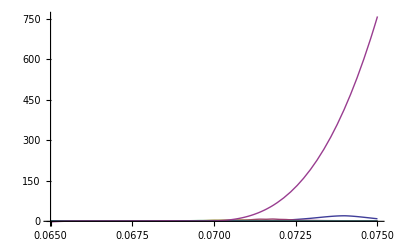

```mathematica
Plot[{i4[v][2][i],i4[v][5][i],i4[v][10][i],i4[v][20][i],i4[v][40][i],i4[v][60][i]},{i,0.065,0.075},PlotRange->Full]
```

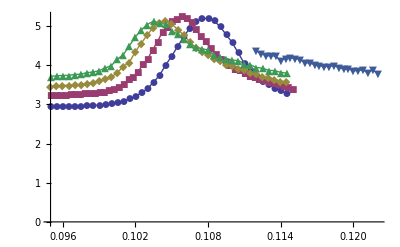

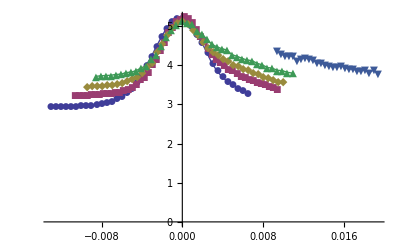

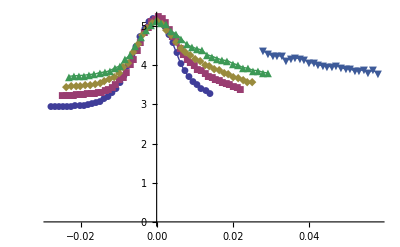

```mathematica
z[v]=0.1;
Do[
Ch4s1[v][l]=Table[{Ch4[v][l][[All,1]][[i]],Log[Ch4[v][l][[All,2]][[i]]]+α[v]*Log[1000*l]},{i,1,Length[Ch4[v][l]]}];

Ch4s2[v][l]=Table[{(Ch4[v][l][[All,1]][[i]]-d0[v]-b2[v]*(l*1000)^(-β2[v])),Log[Ch4[v][l][[All,2]][[i]]]+α[v]*Log[1000*l]},{i,1,Length[Ch4[v][l]]}];

Ch4s[v][l]=Table[{(Ch4[v][l][[All,1]][[i]]-d0[v]-b2[v]*(l*1000)^(-β2[v]))*(l*1000)^z[v],Log[Ch4[v][l][[All,2]][[i]]]+α[v]*Log[1000*l]},{i,1,Length[Ch4[v][l]]}];
,{l,{2,5,10,20,60}}]
pic1=ListPlot[{Ch4s1[v][2],Ch4s1[v][5],Ch4s1[v][10],Ch4s1[v][20],Ch4s1[v][60]},Joined->True,PlotMarkers->Automatic]
pic2=ListPlot[{Ch4s2[v][2],Ch4s2[v][5],Ch4s2[v][10],Ch4s2[v][20],Ch4s2[v][60]},Joined->True,PlotMarkers->Automatic]
pic3=ListPlot[{Ch4s[v][2],Ch4s[v][5],Ch4s[v][10],Ch4s[v][20],Ch4s[v][60]},Joined->True,PlotMarkers->Automatic]
```

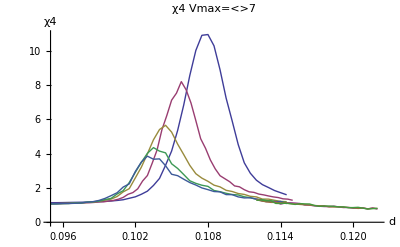

```mathematica
ListLinePlot[{Ch4[v][2],Ch4[v][5],Ch4[v][10],Ch4[v][20],Ch4[v][40],Ch4[v][60],Ch4[v][80],Ch4[v][100]},PlotRange->Full,PlotLabel->"χ4 Vmax="<>v" ",AxesLabel->{"d","χ4"}]
```

{{2000,10.9493},{5000,8.20277},{10000,5.65496},{20000,4.35363},{40000,3.85627}}

{{Log[2000],2.39328},{Log[5000],2.10447},{Log[10000],1.73253},{Log[20000],1.47101},{Log[40000],1.3497}}

{{2000,0.108},{5000,0.1058},{10000,0.1045},{20000,0.1035},{40000,0.103}}

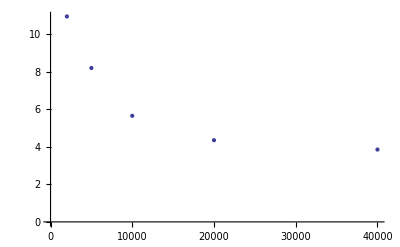

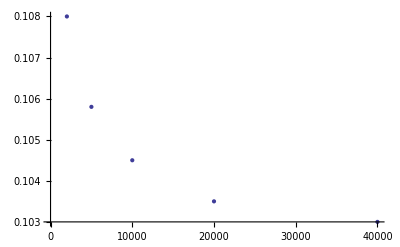

-b0+a0 x

0.101295+c0 x^-ex

{5.19239-0.369005 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.369005 | 0.0310878 | -11.8698 | 0.00128575
b0 | -5.19239 | 0.286789 | -18.1053 | 0.000367541}

{0.101295+0.229882/x^0.464294, | Estimate | Standard Error | t-Statistic | P-Value
ex | 0.464294 | 0.0115651 | 40.1463 | 0.0000340067
c0 | 0.229882 | 0.0220793 | 10.4117 | 0.00189092}

```mathematica
v=7;
maxChi[v]=Table[{l*1000,Max[Ch4[v][l][[All,2]]]},{l,{2,5,10,20,40}}]
LogmaxChi[v]=Table[{Log[maxChi[v][[All,1]][[i]]],Log[maxChi[v][[All,2]][[i]]]},{i,1,Length[maxChi[v]]}]
pmaxChi[v]=Table[{maxChi[v][[All,1]][[i]],Select[Ch4[v][maxChi[v][[All,1]][[i]]/1000],#[[2]]==maxChi[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxChi[v]]}]
ListPlot[maxChi[v]]
ListPlot[pmaxChi[v]]

ClearAll[a0,b0,d0,ex,c0]
model=a0*x-b0
model2=0.10129517685639909+c0*x^(-ex)

nlf1=NonlinearModelFit[LogmaxChi[v],model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]

nlf2=NonlinearModelFit[pmaxChi[v],model2,{ex,c0},x];

nlf2[{"BestFit","ParameterTable"}]
```

```mathematica
ClearAll[a]
```

```mathematica
(*a[7]=0.36900533195753044;
d0[7]=0.08620359557377819;
b0[7]=0.042606612677837816;
ex[v]=-0.09;*)
```

```mathematica
a[7]=0.36900533195753044;
d0[7]=0.10129517685639909;
b0[7]=0.2298823766375316;
ex[v]=-0.46429435895906146;
```

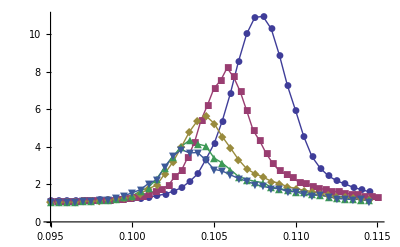

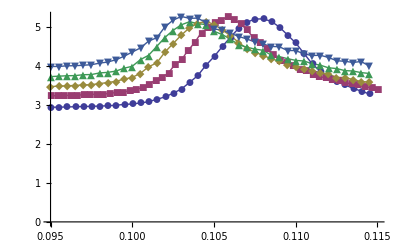

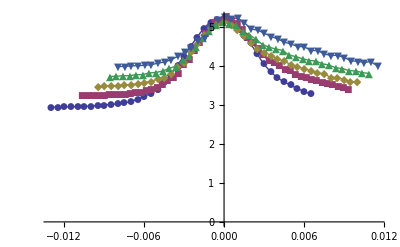

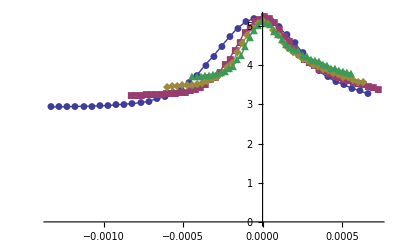

```mathematica
ClearAll[z]
z[v]=-0.3;
Do[
Ch4s1[v][l]=Table[{Ch4[v][l][[All,1]][[i]],Log[Ch4[v][l][[All,2]][[i]]]+a[v]*Log[1000*l]},{i,1,Length[Ch4[v][l]]}];

Ch4s2[v][l]=Table[{Ch4[v][l][[All,1]][[i]]-(d0[v]+b0[v]*(l*1000)^(ex[v])),Log[Ch4[v][l][[All,2]][[i]]]+a[v]*Log[1000*l]},{i,1,Length[Ch4[v][l]]}];

Ch4s[v][l]=Table[{(Ch4[v][l][[All,1]][[i]]-(d0[v]+b0[v]*(l*1000)^(ex[v])))*(1000*l)^z[v],Log[Ch4[v][l][[All,2]][[i]]]+a[v]*Log[1000*l]},{i,1,Length[Ch4[v][l]]}];
,{l,{2,5,10,20,40}}]
pic0=ListPlot[{Ch4[v][2],Ch4[v][5],Ch4[v][10],Ch4[v][20],Ch4[v][40]},Joined->True,PlotMarkers->Automatic,PlotRange->Full]
pic1=ListPlot[{Ch4s1[v][2],Ch4s1[v][5],Ch4s1[v][10],Ch4s1[v][20],Ch4s1[v][40]},Joined->True,PlotMarkers->Automatic]
pic2=ListPlot[{Ch4s2[v][2],Ch4s2[v][5],Ch4s2[v][10],Ch4s2[v][20],Ch4s2[v][40]},Joined->True,PlotMarkers->Automatic]
pic3=ListPlot[{Ch4s[v][2],Ch4s[v][5],Ch4s[v][10],Ch4s[v][20]},Joined->True,PlotMarkers->Automatic]
```

```mathematica
l1=5;
l2=20;
aux=1000;
For[z=-1,z<1,z+=0.05,
ClearAll[i]
dat[l1]=Table[{Ch4s2[v][l1][[All,1]][[i]]*(l1*1000)^z,Ch4s2[v][l1][[All,2]][[i]]},{i,1,Length[Ch4s2[v][l1]]}];
dat[l2]=Table[{Ch4s2[v][l2][[All,1]][[i]]*(l2*1000)^z,Ch4s2[v][l2][[All,2]][[i]]},{i,1,Length[Ch4s2[v][l2]]}];

i[l1]=Interpolation[dat[l1]];
i[l2]=Interpolation[dat[l2]];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]]];

val=Abs[NIntegrate[i[l1][x]-i[l2][x],{x,min,max}]]/(max-min);
Print[val]

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

0.00715

-0.3 = zf